2015 Annual Survey of State Government Finances Lottery Table

Dataset of state lottery finances in 2015

Metadata  |  (Required for public submissions)

"Agriculture" | "Astronomy" | "Chemistry" | "Computational Universe"
"Computer Systems" | "Culture" | "Demographics" | "Earth Science"
"Economics" | "Education" | "Engineering" | "Geography"
"Geometry Data" | "Government" | "Graphics" | "Health"
"Healthcare" | "History" | "Human Activities" | "Images"
"Language" | "Life Science" | "Literature" | "Machine Learning"
"Manufacturing" | "Mathematics" | "Medicine" | "Meteorology"
"Politics" | "Reference" | "Social Media" | "Sociology"
"Statistics" | "Transportation" |  |

"Audio" | "Entity Store" | "Geospatial Data" | "Graphs"
"Image" | "Numerical Data" | "Text" | "Time Series"

DETAILED SOURCE INFORMATION

```mathematica
CloudGet@CloudObject[]
```

Dataset[<>]

$$Object["DefaultContentElement"]="Dataset";

$$Object["FullContent"]=DataResource`$$ContentConversion@
<|
"Dataset"->CloudObject[]
|>;

$$Data=$$Object["FullContent"][$$Object["DefaultContentElement"]];

Resource Examples

"ExampleNotebook": 
Examples added here will be included in the example notebook for the resource and will appear on the webpage for the resource. Give examples, including section headings, text and code. Examples should be self-contained, and the simplest examples should be given first. Browse the Data Repository website for examples.

Use subsection cells to divide examples into groups.
Common section names are "Basic Examples", "Visualization" and "Analysis".
Use text cells to provide a brief explanation of each example.

Use $$Data to represent ResourceData[...].
Use $$Object to represent the completed ResourceObject[...].
Use $$Object["FullContent"] to represent ResourceData[...,All].

Be sure to evaluate definitions of $$Data etc. in the Resource Content section. The $$Data etc. symbols will automatically be replaced by ResourceData[...] or ResourceObject, as appropriate, when the output is built.
The symbols in this notebook, including $$Data, have a local context and will not be defined in the Global context. 

Example code: Histogram[$$Data[All,"col1"]]

### Basic Examples

Retrieve the resource:

```mathematica
$$Object
```

$$Object

Retrieve the default content:

```mathematica
$$Data
```

Dataset[<>]

Lottery income by state:

```mathematica
GeoRegionValuePlot[DeleteMissing@AssociationThread[Normal@$$Data[[All,"State"]] ->Normal@$$Data[[All,"Income"]]]]
```

-Graphics-

Map of per capita lottery income by state:

```mathematica
GeoRegionValuePlot[Module[{states = Normal@$$Data[[All,"State"]],populations,prizes = Normal@$$Data[[All,"Income"]]},
populations= EntityValue[states,"Population"];
If[MatchQ[Last@#,_Missing],Nothing,First@# -> N[(Last@#/#[[2]])]]&/@
Transpose[{states,populations,prizes}]]]
```

-Graphics-

Distribution of lottery proceeds:

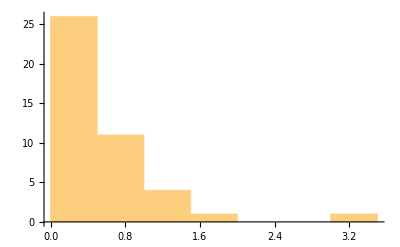

```mathematica
Histogram[Normal@$$Data[[All,"ProceedsAvailable"]]]
```

$$ResourceObject=ResourceObject[EvaluationNotebook[]]

ResourceObject[…]

LocalCache[$$ResourceObject]

CloudDeploy[$$ResourceObject,Permissions→"Private"]

CloudDeploy[$$ResourceObject,Permissions→"Public"]

CloudObject[]

CloudDeploy[$$ResourceObject,"Path",Permissions→"Permissions"]

ResourceSubmit[$$ResourceObject]